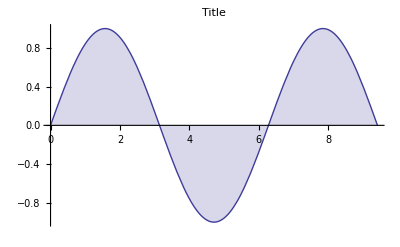

```mathematica
testplot=Plot[Sin[x],{x,0,3 π},Filling->Axis,Frame->{1,1,0,0},FrameLabel->{"x axis","y axis"},PlotLabel->"Title"]
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "blogit" ]
```

```mathematica
peeters`exportForLatex["bb", testplot]
```

{bb.eps,bbpn.png}

```mathematica
peeters`exportForLatex::usage
```

This seems to be the most compact way to export for latex that still retains good resolution.  Use the epstopdf program to convert the resulting .eps file.  Also generate a .png for wordpress posts at the same time. 
Note that the .png displays with some software having a checkerboard background, but that doesn't show up in the eventual web view.

This png file is generated with a different basename so that latex includegraphics doesn't find it.

```mathematica
.
```

```mathematica
peeters`lblPlot::usage
```

Clear[f, r]
f[r_] := 4 r/(1 - r)^2
i[r_, delta_] := 1/(1 + f[r] Sin[delta/2]^2)
s = Plot[Evaluate@Table[i[r, d], {r, {.1, .3, .6, .97}}], {d, 0, 4 Pi}, PlotRange -> {0, 1}];
lblPlot[s, {FontFamily -> "xkcd", 16}]

```mathematica
(*Clear[f, r]
f[r_] := 4 r/(1 - r)^2
i[r_, delta_] := 1/(1 + f[r] Sin[delta/2]^2)
s = Plot[Evaluate@Table[i[r, d], {r, {.1, .3, .6, .97}}], {d, 0, 4 Pi}, PlotRange -> {0, 1}];
peeters`lblPlot[s(*, {FontFamily -> \"xkcd\", 16}*)]  *)
```